# Differentiation tests

## Gradientti

## 2d

```mathematica
f[x_, y_]:= x^2 y
```

```mathematica
Grad[f[x, y], {x, y}]
```

{2 x y,x^2}

```mathematica
% /.{x->3, y -> 2 }
```

{12,9}

## 3d

```mathematica
V[x_, y_, z_]:= 2 x^2 + 3y ^2 - 4 z ; 
Grad[V[x, y, z], {x, y, z}]
```

{4 x,6 y,-4}

```mathematica
field[x_, y_, z_]:= {4 x,6 y,-4}
field[0,0,0]
field[1,2,3]
```

{0,0,-4}

{4,12,-4}

## 4d

```mathematica
V[x_, y_, z_, w_] :=  2 x^2 + 3y ^2 - 4 z+ w^3
Grad[V[x, y, z, w], {x, y, z, w}]
```

{4 x,6 y,-4,3 w^2}

```mathematica
field4d[x_, y_, z_, w_]:= {4 x,6 y,-4,3 w^2}; 
field4d[0,0,0,0]
field4d[2,4,10,10]
```

{0,0,-4,0}

{8,24,-4,300}

## 5d

```mathematica
V[x_, y_, z_, w_, w2_] :=  2 x^2 + 3y ^2 - 4 z+ w^3+ w2^4
Grad[V[x, y, z, w, w2], {x, y, z, w, w2}]
```

{4 x,6 y,-4,3 w^2,4 w2^3}

```mathematica
field4d[x_, y_, z_, w_, w2_]:= {4 x,6 y,-4,3 w^2,4 w2^3}; 
field4d[0,0,0,0, 0]
field4d[2,4,10,15, 14]
```

{0,0,-4,0,0}

{8,24,-4,675,10976}

## Derivaatta

```mathematica
g[x_] := x^2 
D[g[x], x]
```

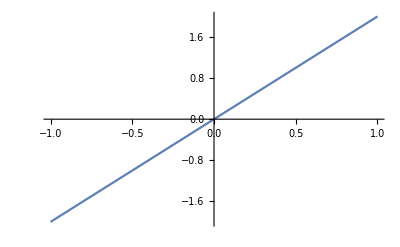

```mathematica
Plot[2 x,{x,-1,1}]
```

## Laplacian

## Laplacian 2d

```mathematica
Laplacian[f[x, y], {x, y}]
```

2 y

```mathematica
2
```

## Laplacian 3d

```mathematica
V[x_, y_, z_]:= 2 x^2 + 3y ^2 - 4 z ; 
Laplacian[V[x, y, z], {x, y, z}]
```

10